#### BC_MSAT_DREX_tests.nb (formerly ES_voight2betas.nb) Input Cvoigt, output a lattice diagram as well as the closest XISO as T_XISO and Cvoigt_XISO Evaluate common_funs.nb, ES_FindSymGroups.nb, BC_ChooseTmat.nb before running this notebook. Carl Tape, ctape@alaska.edu, June 2023

#### Settings. Set WantDetails="WantDetails" if you want the full output,including figures and text like T is assigned symmetry of at least XISO. If you want faster calculations, use WantDetails="NoWantDetails".

```mathematica
xeps=10^-7;
reps=0.1;
WantDetails="NoWantDetails";
```

#### Choose an example for the rest of the notebook (Here this needs to be Igel for comparison with other maps listed below.)

```mathematica
Cmat = CmatIgel;
```

#### Convert from Voigt to BB (this is already done in BC_ChooseTmat.nb for several example maps)

```mathematica
Tmat = Simplify[TmatOfCmat[Cmat]];
```

#### Check symmetry and display output (including for the closest ISO)

```mathematica
Tmat==Transpose[Tmat]
MatrixNote[Tmat]
PrintVoigt[Tmat]
```

True

T is Igel

The [T]_𝔹𝔹 matrix is (10. | 0.7 | 1.05 | 5.2 | -3.92598 | -3.10269
0.7 | 8. | -2. | -0.2 | -0.46188 | 0.326599
1.05 | -2. | 6. | -0.45 | -0.190526 | 0.318434
5.2 | -0.2 | -0.45 | 5.5 | 0 | -1.22474
-3.92598 | -0.46188 | -0.190526 | 0 | 5.5 | 2.12132
-3.10269 | 0.326599 | 0.318434 | -1.22474 | 2.12132 | 13.)

The eigenvalues are: {17.7924,10.1797,9.22349,5.83219,4.30288,0.669364}

The Voigt matrix is (10. | 3.5 | 2.5 | -5. | 0.1 | 0.3
3.5 | 8. | 1.5 | 0.2 | -0.1 | -0.15
2.5 | 1.5 | 6. | 1. | 0.4 | 0.24
-5. | 0.2 | 1. | 5. | 0.35 | 0.525
0.1 | -0.1 | 0.4 | 0.35 | 4. | -1.
0.3 | -0.15 | 0.24 | 0.525 | -1. | 3.)

3-2-2024 7:43

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 12.0102   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.533 = 30.55^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (7. | 0. | 0. | 0. | 0. | 0.
0. | 7. | 0. | 0. | 0. | 0.
0. | 0. | 7. | 0. | 0. | 0.
0. | 0. | 0. | 7. | 0. | 0.
0. | 0. | 0. | 0. | 7. | 0.
0. | 0. | 0. | 0. | 0. | 13.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 2. and μ = 3.5, bulk modulus κ = 4.33333, Poisson ratio = 0.181818

#### Igel1995 XISO approximation via DREX (note: this C is not XISO because the rotation matrix used in DREX is not a true rotation matrix)

rotation matrix from DREX (this is the DREX output file SCC.txt written out by Carl)

```mathematica
RmatIgeldrex=({{0.95096537099, 0.26674327873, 0.15656591722}, {-0.26657423196, 0.92199545424, -0.28082478741}, {-0.32116510346, 0.15223361177, 0.93470738938}});
```

determinant is not =1

```mathematica
Det[RmatIgeldrex]
```

0.990722

```mathematica
MatrixForm[RmatIgeldrex.Transpose[RmatIgeldrex]]
MatrixForm[Transpose[RmatIgeldrex].RmatIgeldrex]
```

(1. | -0.0515344 | -0.118466
-0.0515344 | 1. | -0.036516
-0.118466 | -0.036516 | 1.)

(1.07854 | -0.0410087 | -0.076446
-0.0410087 | 0.944403 | -0.0748624
-0.076446 | -0.0748624 | 0.977053)

this rotates Cxiso by R (which is assumed to be the incorrect operation)

```mathematica
CmatIgelXISOdrex=({{10.0324, 4.1541, 1.6201, 0.6990, -1.3339, -0.4753}, {4.1541, 9.9216, 1.4184, -0.0860, -0.9307, -0.4689}, {1.6201, 1.4184, 7.1859, 0.2859, -1.4454, 0.1922}, {0.6990, -0.0860, 0.2859, 3.7104, -0.1995, -0.2195}, {-1.3339, -0.9307, -1.4454, -0.1995, 3.9309, -0.3309}, {-0.4753, -0.4689, 0.1922, -0.2195, -0.3309, 2.9321}});
```

this rotates Cxiso by R^T (which is assumed to be the correct operation)

```mathematica
CmatIgelXISOdrex=({{11.4995, 4.1701, 1.4242, -0.7860, -0.4700, -0.3843}, {4.1701, 8.9480, 1.4170, -0.8420, 0.5925, -0.3445}, {1.4242, 1.4170, 6.7659, -1.0114, 0.0169, 0.2105}, {-0.7860, -0.8420, -1.0114, 3.5720, -0.1154, -0.4766}, {-0.4700, 0.5925, 0.0169, -0.1154, 3.9041, -0.1018}, {-0.3843, -0.3445, 0.2105, -0.4766, -0.1018, 2.9984}});
```

```mathematica
CmatIgelXISOdrex==Transpose[CmatIgelXISOdrex]
TmatIgelXISOdrex = Simplify[TmatOfCmat[CmatIgelXISOdrex]];
```

True

#### Igel1995 XISO approximation via MSAT

```mathematica
CmatIgelXISOmsat=({{9.6730, 2.6077, 2.8305, -0.1210, -0.1869, -0.4260}, {2.6077, 8.4039, 1.0912, 0.1360, 0.2310, 0.9131}, {2.8305, 1.0912, 7.8645, 0.1570, 0.4624, 0.6675}, {-0.1210, 0.1360, 0.1570, 3.5198, 0.1597, 0.0082}, {-0.1869, 0.2310, 0.4624, 0.1597, 3.9358, -0.1967}, {-0.4260, 0.9131, 0.6675, 0.0082, -0.1967, 3.5737}});
CmatIgelXISOmsat==Transpose[CmatIgelXISOmsat]
TmatIgelXISOmsat = Simplify[TmatOfCmat[CmatIgelXISOmsat]];
```

True

#### Igel1995 XISO approximation via MSAT (with stiff option)

```mathematica
CmatIgelXISOmsatstiff=({{10.9382, 3.7136, 1.1242, -3.2946, 0.3394, 0.2313}, {3.7136, 8.0504, 1.3834, -1.2978, 0.1810, 0.1002}, {1.1242, 1.3834, 7.5688, 0.6850, -0.0776, -0.0298}, {-3.2946, -1.2978, 0.6850, 5.3463, -0.2975, -0.2118}, {0.3394, 0.1810, -0.0776, -0.2975, 2.7551, 0.1719}, {0.2313, 0.1002, -0.0298, -0.2118, 0.1719, 2.6200}});
CmatIgelXISOmsatstiff==Transpose[CmatIgelXISOmsatstiff]
TmatIgelXISOmsatstiff = Simplify[TmatOfCmat[CmatIgelXISOmsatstiff]];
```

True

#### Igel1995 XISO approximation via Brandon VanderBeek codes

```mathematica
CmatIgelXISOvdb=({{9.7300, 2.2092, 2.0165, -0.6482, -0.6781, -0.5848}, {2.2092, 8.4402, 1.8344, 0.4718, 0.1912, 1.1227}, {2.0165, 1.8344, 8.7097, 0.4344, 1.1988, 0.0759}, {-0.6482, 0.4718, 0.4344, 3.2473, 0.1319, 0.2561}, {-0.6781, 0.1912, 1.1988, 0.1319, 3.5635, -0.6247}, {-0.5848, 1.1227, 0.0759, 0.2561, -0.6247, 3.7492}});
CmatIgelXISOvdb==Transpose[CmatIgelXISOvdb]
TmatIgelXISOvdb = Simplify[TmatOfCmat[CmatIgelXISOvdb]];
```

True

## Closest maps

#### Find closest elastic maps to each symmetry class

```mathematica
OutputFor[Tmat,MONO]
OutputFor[Tmat,ORTH]
OutputFor[Tmat,TET]
OutputFor[Tmat,CUBE]
OutputFor[Tmat,XISO]
OutputFor[Tmat,TRIG]
OutputFor[Tmat,ISO]
```

3-2-2024 7:43

NMinimize = {1.77381,{θ→6.2378,σ→-1.04197,ϕ→1.58615}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {357.4,0.,90.9})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.0153358 | 0.0453676 | 0.998853
0.000696467 | 0.99897 | -0.0453622
-0.999882 | 0 | -0.0153516)  (A MONO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

β_MONO^T = 0.075 = 4.31^o (Angle between T and 𝒯_MONO)

3-2-2024 7:43

NMinimize = {2.87693,{θ→1.50411,σ→1.59241,ϕ→0.745272}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_ORTH(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {86.2,91.2,42.7})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.998603 | -0.0273918 | 0.0451902
0.0507699 | -0.734539 | 0.676665
0.0146589 | 0.678013 | 0.734903)  (A ORTH-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_ORTH(U)))

β_ORTH^T = 0.122 = 6.99^o (Angle between T and 𝒯_ORTH)

3-2-2024 7:43

NMinimize = {3.35528,{θ→1.4968,σ→0.0253455,ϕ→0.738956}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {85.8,1.5,42.3})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0293571 | -0.998328 | 0.0497941
0.738786 | 0.0552263 | 0.671673
-0.6733 | 0.0170688 | 0.739172)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

β_TET^T = 0.142 = 8.16^o (Angle between T and 𝒯_TET)

3-2-2024 7:43

NMinimize = {8.23431,{θ→1.49874,σ→0.810614,ϕ→0.774284}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_CUBE(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {85.9,46.4,44.4})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.687363 | -0.724568 | 0.0503407
0.543518 | -0.467157 | 0.69739
-0.481789 | 0.506721 | 0.714922)  (A CUBE-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_CUBE(U)))

β_CUBE^T = 0.356 = 20.4^o (Angle between T and 𝒯_CUBE)

3-2-2024 7:43

NMinimize = {6.50485,{θ→1.50483,σ→3.07695,ϕ→0.714334}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {86.2,0.,40.9})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0498003 | -0.997825 | 0.0431815
0.753887 | 0.0659144 | 0.65369
-0.655115 | 0 | 0.75553)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

β_XISO^T = 0.279 = 15.98^o (Angle between T and 𝒯_XISO)

3-2-2024 7:43

NMinimize = {6.0697,{θ→4.65869,σ→-0.107489,ϕ→2.47124}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TRIG(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {266.9,-6.2,141.6})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.0653149 | 0.997307 | -0.0333426
0.783718 | 0.0305863 | -0.620363
-0.617673 | -0.0666501 | -0.783606)  (A TRIG-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TRIG(U)))

β_TRIG^T = 0.26 = 14.89^o (Angle between T and 𝒯_TRIG)

3-2-2024 7:44

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 12.0102   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.533 = 30.55^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (7. | 0. | 0. | 0. | 0. | 0.
0. | 7. | 0. | 0. | 0. | 0.
0. | 0. | 7. | 0. | 0. | 0.
0. | 0. | 0. | 7. | 0. | 0.
0. | 0. | 0. | 0. | 7. | 0.
0. | 0. | 0. | 0. | 0. | 13.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 2. and μ = 3.5, bulk modulus κ = 4.33333, Poisson ratio = 0.181818

#### Lattice diagram

ChopT = 0.01^o

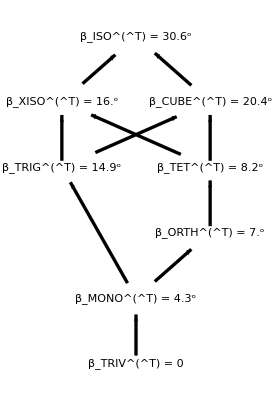

```mathematica
LatticeOfDTs[Tmat]
```

#### Closest maps

#### The ordering here follows BC2004: TRIV-MONO-ORTH-TET-XISO-ISO, with CUBE and TRIG (not considered in BC2004) added at the end.

```mathematica
TmatTRIV =closest[1]=Chop[ProjToVSigOfU[Tmat,UT[Tmat,TRIV],TRIV],xeps];
TmatMONO =closest[2]=Chop[ProjToVSigOfU[Tmat,UT[Tmat,MONO],MONO],xeps];
TmatORTH =closest[3]=Chop[ProjToVSigOfU[Tmat,UT[Tmat,ORTH],ORTH],xeps];
TmatTET   =closest[4]=Chop[ProjToVSigOfU[Tmat,UT[Tmat,TET],TET],xeps];
TmatXISO =closest[5]=Chop[ProjToVSigOfU[Tmat,UT[Tmat,XISO],XISO],xeps];
TmatISO   =closest[6]=Chop[ProjToVSigOfU[Tmat,UT[Tmat,ISO],ISO],xeps];
TmatCUBE =closest[7]=Chop[ProjToVSigOfU[Tmat,UT[Tmat,CUBE],CUBE],xeps];
TmatTRIG =closest[8]=Chop[ProjToVSigOfU[Tmat,UT[Tmat,TRIG],TRIG],xeps];
```

```mathematica
table=Table[Table[Round[AngleMatrix[closest[i],closest[j]]/Degree,reps],{i,8}],{j,8}]
```

{{0.,4.3,7.,8.2,16.,30.6,20.4,14.9},{4.3,0.,5.5,7.,15.4,30.3,20.,14.5},{7.,5.5,0.,4.3,14.6,29.8,19.3,15.7},{8.2,7.,4.3,0.,14.,29.5,19.,15.3},{16.,15.4,14.6,14.,0.,26.4,24.6,7.},{30.6,30.3,29.8,29.5,26.4,0.,23.3,27.},{20.4,20.,19.3,19.,24.6,23.3,0.,25.3},{14.9,14.5,15.7,15.3,7.,27.,25.3,0.}}

```mathematica
SigText[0]="";
SigText[1]=TRIV;
SigText[2]=MONO;
SigText[3]=ORTH;
SigText[4]=TET;
SigText[5]=XISO;
SigText[6]=ISO;
SigText[7]=CUBE;
SigText[8]=TRIG;
```

```mathematica
rrow[i_]:=Join[{{SigText[i]}},table[[i]]];
rrow[0]:=Join[{""},Table[SigText[i],{i,8}]];
rrow[0]
rrow[3]
```

{,TRIV,MONO,ORTH,TET,XISO,ISO,CUBE,TRIG}

{{ORTH},7.,5.5,0.,4.3,14.6,29.8,19.3,15.7}

```mathematica
TableForm[Table[rrow[i],{i,0,8}],TableSpacing->{5,2}]
```

| TRIV | MONO | ORTH | TET | XISO | ISO | CUBE | TRIG
TRIV | 0. | 4.3 | 7. | 8.2 | 16. | 30.6 | 20.4 | 14.9
MONO | 4.3 | 0. | 5.5 | 7. | 15.4 | 30.3 | 20. | 14.5
ORTH | 7. | 5.5 | 0. | 4.3 | 14.6 | 29.8 | 19.3 | 15.7
TET | 8.2 | 7. | 4.3 | 0. | 14. | 29.5 | 19. | 15.3
XISO | 16. | 15.4 | 14.6 | 14. | 0. | 26.4 | 24.6 | 7.
ISO | 30.6 | 30.3 | 29.8 | 29.5 | 26.4 | 0. | 23.3 | 27.
CUBE | 20.4 | 20. | 19.3 | 19. | 24.6 | 23.3 | 0. | 25.3
TRIG | 14.9 | 14.5 | 15.7 | 15.3 | 7. | 27. | 25.3 | 0.

#### Checks on angles listed in the lattice (this is the top row of the table)

```mathematica
Print["beta(T,MONO) = ",(Round[AngleMatrix[Tmat,TmatMONO] /Degree,reps])^o];
Print["beta(T,ORTH) = ",(Round[AngleMatrix[Tmat,TmatORTH] /Degree,reps])^o];
Print["beta(T,TET) = ",(Round[AngleMatrix[Tmat,TmatTET] /Degree,reps])^o];
Print["beta(T,XISO) = ",(Round[AngleMatrix[Tmat,TmatXISO] /Degree,reps])^o];
Print["beta(T,ISO) = ",(Round[AngleMatrix[Tmat,TmatISO] /Degree,reps])^o];
Print["beta(T,CUBE) = ",(Round[AngleMatrix[Tmat,TmatCUBE] /Degree,reps])^o];
Print["beta(T,TRIG) = ",(Round[AngleMatrix[Tmat,TmatTRIG] /Degree,reps])^o];
```

beta(T,MONO) = 4.3^o

beta(T,ORTH) = 7.^o

beta(T,TET) = 8.2^o

beta(T,XISO) = 16.^o

beta(T,ISO) = 30.6^o

beta(T,CUBE) = 20.4^o

beta(T,TRIG) = 14.9^o

#### Closest XISO: Double-check that TmatXISO is indeed XISO

```mathematica
TmatXISO =Closest[Tmat,XISO];
OutputFor[TmatXISO,XISO]
```

3-2-2024 7:44

NMinimize = {6.03787×10^-9,{θ→1.50483,σ→1.41779,ϕ→0.714334}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {86.2,0.,40.9})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0498003 | -0.997825 | 0.0431815
0.753887 | 0.0659144 | 0.65369
-0.655115 | 0 | 0.75553)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

β_XISO^T = 0 (Angle between T and 𝒯_XISO. The initial β_XISO^T = 2.66×10^-10 is here chopped to zero, since the chop threshold is set at 0.01^o)

Since β_XISO^T = 0, T is assigned symmetry at least XISO.

```mathematica
PrintVoigt[TmatXISO]
```

The [T]_𝔹𝔹 matrix is (12.0284 | 0.456493 | 0.397549 | 3.07421 | -2.91164 | -3.27377
0.456493 | 5.14803 | 0.181413 | 0.182489 | -0.192338 | -0.216259
0.397549 | 0.181413 | 5.09532 | 0.166797 | -0.150986 | -0.187109
3.07421 | 0.182489 | 0.166797 | 6.33018 | -1.13784 | -1.41006
-2.91164 | -0.192338 | -0.150986 | -1.13784 | 6.39812 | 1.36334
-3.27377 | -0.216259 | -0.187109 | -1.41006 | 1.36334 | 13.)

The eigenvalues are: {17.7206,9.89733,5.25329,5.25329,4.93777,4.93777}

The Voigt matrix is (11.0157 | 2.87728 | 1.79801 | -3.71414 | -0.235055 | -0.203371
2.87728 | 7.39922 | 1.96056 | -0.639923 | -0.052566 | -0.0365741
1.79801 | 1.96056 | 7.31338 | 0.344527 | 0.0227588 | 0.0107847
-3.71414 | -0.639923 | 0.344527 | 6.01418 | 0.228246 | 0.198775
-0.235055 | -0.052566 | 0.0227588 | 0.228246 | 2.57402 | 0.0907067
-0.203371 | -0.0365741 | 0.0107847 | 0.198775 | 0.0907067 | 2.54766)

3-2-2024 7:44

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 10.0962   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.461 = 26.39^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (7. | 0. | 0. | 0. | 0. | 0.
0. | 7. | 0. | 0. | 0. | 0.
0. | 0. | 7. | 0. | 0. | 0.
0. | 0. | 0. | 7. | 0. | 0.
0. | 0. | 0. | 0. | 7. | 0.
0. | 0. | 0. | 0. | 0. | 13.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 2. and μ = 3.5, bulk modulus κ = 4.33333, Poisson ratio = 0.181818

#### Check beta calculation (this should be the angle at the top of the lattice)

```mathematica
AngleMatrix[Tmat,Closest[Tmat,ISO]] /Degree
βT[Tmat,ISO]/Degree
```

30.5521

30.5521

## Compare results with those from MSAT and VanderBeek [Igel1995 example]

```mathematica
TmatXISOdrex = TmatIgelXISOdrex;
TmatXISOmsat = TmatIgelXISOmsat;
TmatXISOmsatstiff = TmatIgelXISOmsatstiff;
TmatXISOvdb = TmatIgelXISOvdb;
```

#### Check whether the XISO-approx results are XISO maps (the DREX version fails because the U from DREX is not a true rotation matrix)

```mathematica
OutputFor[TmatXISOdrex,XISO]
```

3-2-2024 7:44

NMinimize = {3.03854,{θ→1.69242,σ→-0.944915,ϕ→0.366511}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {97.,0.,21.})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.113266 | -0.992613 | -0.0434776
0.926687 | -0.121324 | 0.355713
-0.35836 | 0 | 0.933583)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

β_XISO^T = 0.142 = 8.11^o (Angle between T and 𝒯_XISO)

```mathematica
OutputFor[TmatXISOmsat,XISO]
```

3-2-2024 7:44

NMinimize = {0.000197095,{θ→0.327334,σ→2.004,ϕ→1.43068}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {18.8,0.,82.})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.132247 | -0.32152 | 0.937622
0.0449044 | 0.946903 | 0.318369
-0.990199 | 0 | 0.139663)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

β_XISO^T = 0 (Angle between T and 𝒯_XISO. The initial β_XISO^T = 9.5×10^-6 is here chopped to zero, since the chop threshold is set at 0.01^o)

Since β_XISO^T = 0, T is assigned symmetry at least XISO.

```mathematica
OutputFor[TmatXISOmsatstiff,XISO]
```

3-2-2024 7:45

NMinimize = {0.000168933,{θ→1.68364,σ→2.28465,ϕ→0.601153}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {96.5,0.,34.4})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.0928642 | -0.99364 | -0.0636891
0.819439 | -0.112606 | 0.561996
-0.565593 | 0 | 0.824684)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

β_XISO^T = 0 (Angle between T and 𝒯_XISO. The initial β_XISO^T = 7.5×10^-6 is here chopped to zero, since the chop threshold is set at 0.01^o)

Since β_XISO^T = 0, T is assigned symmetry at least XISO.

```mathematica
OutputFor[TmatXISOvdb,XISO]
```

3-2-2024 7:45

NMinimize = {0.000214678,{θ→0.34763,σ→1.40324,ϕ→1.19456}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {19.9,0.,68.4})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.345442 | -0.34067 | 0.874422
0.125169 | 0.940183 | 0.316842
-0.930055 | 0 | 0.36742)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

β_XISO^T = 0 (Angle between T and 𝒯_XISO. The initial β_XISO^T = 0.0000103 is here chopped to zero, since the chop threshold is set at 0.01^o)

Since β_XISO^T = 0, T is assigned symmetry at least XISO.

#### Example: MSAT vs ours

```mathematica
MatrixForm[TmatXISO]
MatrixForm[TmatXISOmsat]
Print["beta(XISO,MSAT) = ",(Round[AngleMatrix[TmatXISO,TmatXISOmsat] /Degree,reps])^o];
Print["beta(T,MSAT) = ",(Round[AngleMatrix[Tmat,TmatXISOmsat] /Degree,reps])^o];
```

(12.0284 | 0.456493 | 0.397549 | 3.07421 | -2.91164 | -3.27377
0.456493 | 5.14803 | 0.181413 | 0.182489 | -0.192338 | -0.216259
0.397549 | 0.181413 | 5.09532 | 0.166797 | -0.150986 | -0.187109
3.07421 | 0.182489 | 0.166797 | 6.33018 | -1.13784 | -1.41006
-2.91164 | -0.192338 | -0.150986 | -1.13784 | 6.39812 | 1.36334
-3.27377 | -0.216259 | -0.187109 | -1.41006 | 1.36334 | 13.)

(7.0396 | 0.3194 | 0.0164 | 0.257 | -0.172628 | 0.140437
0.3194 | 7.8716 | -0.3934 | 0.4179 | -0.508472 | 0.413556
0.0164 | -0.3934 | 7.1474 | 1.3391 | -0.489535 | 0.942727
0.257 | 0.4179 | 1.3391 | 6.43075 | 0.637828 | -1.22817
-0.172628 | -0.508472 | -0.489535 | 0.637828 | 6.51058 | 0.858333
0.140437 | 0.413556 | 0.942727 | -1.22817 | 0.858333 | 13.0001)

beta(XISO,MSAT) = 26.8^o

beta(T,MSAT) = 28.8^o

#### Comparison among all versions

```mathematica
cmaps[1]=Tmat;
cmaps[2]=TmatXISO;
cmaps[3]=TmatXISOdrex;
cmaps[4]=TmatXISOmsat;
cmaps[5]=TmatXISOmsatstiff;
cmaps[6]=TmatXISOvdb;
```

```mathematica
tablex=Table[Table[Round[AngleMatrix[cmaps[i],cmaps[j]]/Degree,reps],{i,6}],{j,6}]
```

{{0.,16.,28.6,28.8,18.5,27.8},{16.,0.,24.3,26.8,9.6,26.8},{28.6,24.3,0.,16.6,21.1,20.4},{28.8,26.8,16.6,0.,25.6,10.},{18.5,9.6,21.1,25.6,0.,26.6},{27.8,26.8,20.4,10.,26.6,0.}}

```mathematica
SigText[0]="";
SigText[1]=T;
SigText[2]=XISO;
SigText[3]=DREX;
SigText[4]=MSAT;
SigText[5]=MSATstiff;
SigText[6]=VDB;
```

```mathematica
rrow[i_]:=Join[{{SigText[i]}},tablex[[i]]];
rrow[0]:=Join[{""},Table[SigText[i],{i,6}]];
```

```mathematica
TableForm[Table[rrow[i],{i,0,6}],TableSpacing->{5,2}]
```

| T | XISO | DREX | MSAT | MSATstiff | VDB
T | 0. | 16. | 28.6 | 28.8 | 18.5 | 27.8
XISO | 16. | 0. | 24.3 | 26.8 | 9.6 | 26.8
DREX | 28.6 | 24.3 | 0. | 16.6 | 21.1 | 20.4
MSAT | 28.8 | 26.8 | 16.6 | 0. | 25.6 | 10.
MSATstiff | 18.5 | 9.6 | 21.1 | 25.6 | 0. | 26.6
VDB | 27.8 | 26.8 | 20.4 | 10. | 26.6 | 0.